```mathematica
SetDirectory[NotebookDirectory[]];
Get["Packages\\TextbookFigurePreamble.wl"] ;
Get["LatticePhyllotaxis`",Path->FileNameJoin[PersistentSymbol["persistentGitHubPath"],"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

## Setup

```mathematica
figureStyle = jStyle
jParastichyColour[n_] := figureStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->figureStyle["FontFamily"],FontSize->n};


getTextbookData[name_] := Module[{data=PersistentSymbol["TextbookData"] },data[name]];
setTextbookData[name_,value_] := Module[{data},
data=PersistentSymbol["TextbookData"] ;
data = Append[data,name->value];
PersistentSymbol["TextbookData"] = data;
];
rebuildingData = False;
If[rebuildingData,PersistentSymbol["TextbookData"] =<||>]
```

<|CylinderColour→RGBColor[0.8692074837412045, 0.86, 0.6466894826847229],CylinderColour3D→RGBColor[0.6953659869929636, 0.888, 0.5173515861477783],FontFamily→Times,DisplayFontFamily→Gill Sans MT,FullWidthImagePT→333,ParastichyColour→<|1→RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],2→RGBColor[0.4687348547943994, 0.29473626986998797, 0.5955133155492501],3→RGBColor[0.4518714536621338, 0.549629484806721, 0.24743503166788056],4→RGBColor[0.955983350983375, 0.9459627980758899, 0.942555568392974],5→RGBColor[0.2138260590152513, 0.18751247299324145, 0.15071362998820095]|>,ArrowheadSpec→0.02|>

```mathematica
PersistentSymbol["TextbookData"] =<||>
```

<||>

```mathematica
exportFigures := {
jExport[Ch5Transition];
jExport[Ch5Transforms];
jExport[Ch5PineSet];
jExport[Ch5FibScalingBar];
jExport[Ch5Bulge4];
}
shExport[x_] := x;
```

```mathematica
(*exportFigures*)
```

## ch5fibscaling

```mathematica
fpair[n_] := {Fibonacci[n],Fibonacci[n+1]};
data=Map[<|"n"->#, "pair"-> fpair[#],"pairText"->pairToText[fpair[#]], "rise"->1/(Last@vanItersonLabelPoint[fpair[#]])|>&,Table[n,{n,0,11}]] ;
```

```mathematica
pairToText[{m_,n_}] :=  Style[StringTemplate["(``,``)"][m,n],jFont[Scaled[0.03]]];
Ch5FibScalingBar := Module[{},
Show[ListLogPlot[Map[{First[#["pair"]],#["rise"]}& ,data],BaseStyle->setGill,
PlotStyle->jParastichyColour[1]
,PlotRange->{{-10,110},{0.5,10^5}}
,Frame->{{True,False},{True,False}},
FrameLabel->{"Fibonacci count" ,"Inverse Rise"},FrameTicks->{{Automatic,None},{{0,89},None}}]
,Graphics[Map[Text[#["pairText"],{First[#["pair"]],Log[#["rise"]]},{-1.5,0}]&,data]]
]
]
```

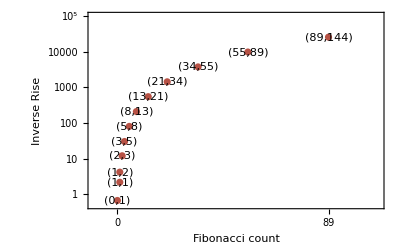

```mathematica
Ch5FibScalingBar
```

## Ch5Transition

This creates and uses a StemStretch function stored in the lattice
recall  latticePoints[lattice_,scalingFunction_] :=  Map[latticeScaling[lattice,scalingFunction],latticePoints[lattice]]

### Rise stretches

```mathematica
(* a rise scaling  *)
(*linearRiseScalingFallCylinderZ[cylinderLU_,targetz_] :=    Module[{z,eps = 10^-1},
z=  (targetz-cylinderLU[[1]])/(cylinderLU[[2]]-cylinderLU[[1]]);
(  (1-z)  + eps (z))
];
*)
scaleZ01ToCylinder[cylinderLU_,bulgeFunction_] := Module[{zScale},
zScale[cylinderZ_] :=   (cylinderZ-cylinderLU[[1]])/(cylinderLU[[2]]-cylinderLU[[1]]);
Composition[bulgeFunction,zScale]
];
linearRiseFallZ01[z_] :=    Module[{eps = 10^-1},(  (1-z)  + eps (z))];
linearRiseFallZLattice[lattice_,z_] :=    scaleZ01ToCylinder[latticeGetCylinderLU[lattice],linearRiseFallZ01][z];
quadraticRiseFallZLattice[lattice_,z_] := linearRiseFallZLattice[lattice,z]^2;

riseByUnscaledHeightFunction[lattice_] := Module[{heightsBase,risesStretch},
heightsBase =  Drop[Last/@latticePoints[lattice],-1];
risesStretch = Differences[Last/@ latticePoints[lattice,"StemStretch"]];
Interpolation[Transpose[{heightsBase,risesStretch}]]
];

inverseriseByUnscaledHeightFunction[lattice_] := Function[{z},1/riseByUnscaledHeightFunction[lattice][z]];
```

```mathematica
(*
riseScalingZCylinder has domain of the z-values of the nodeCylinder (say [0,4] )
Typically riseScalingZCylinder[0]=1, and values higher are the proportions by which the rises are to be stretched

*)
makeLatticeStretchFunction[baseLattice_,riseScalingZCylinder_] := Module[{nodeHeights,targetRiseAtNode,targetNodeHeights,heightScalingAtNodes,latticeScalingFunction,scaledLattice},
nodeHeights = Map[Last,latticePoints[baseLattice]];
targetRiseAtNode = latticeRise[baseLattice]* Map[riseScalingZCylinder,nodeHeights];
targetNodeHeights = Prepend[Drop[Accumulate[targetRiseAtNode],-1],0];
heightScalingAtNodes = Interpolation[Transpose[{nodeHeights,targetNodeHeights}]];
heightScalingAtNodes
];

(*
riseScalingZCylinder has domain [cylinderLU]
*)

makeStretchedLattice[baseLattice_,riseScalingZCylinder_] := Module[{latticeZScalingFunction,latticeScalingFunction,scaledLattice,cylinder,scaledCylinder},
(*riseScalingZCylinder[z_] := riseScaling[latticeGetCylinderLU[baseLattice],z];
*)
latticeZScalingFunction = makeLatticeStretchFunction[baseLattice,riseScalingZCylinder];
latticeScalingFunction = Function[{xz},{xz[[1]],latticeZScalingFunction[xz⟦2⟧]}];
scaledLattice = baseLattice;
scaledLattice = latticeSetScaling[scaledLattice,"StemStretch"->latticeScalingFunction];
(*latticeScalingFunction maps x,z to x,z *)
scaledCylinder = Transpose[ latticeScalingFunction /@ Transpose[latticeGetCylinder[baseLattice]] ];
scaledLattice = latticeSetDisplayCylinder[scaledLattice,scaledCylinder];
scaledLattice
];
```

### Display code

```mathematica
showStem[lattice_,p2ThroughList_,chains_] := Module[{chainColour},
chainColour = <|"Up"->jParastichyColour[1],"Down"->jParastichyColour[2]|>;
chainColour = <|"Up"->Gray,"Down"->Gray|>;

Show[
Graphics[
{
figureStyle["CylinderColour"],
Rectangle@@Transpose[latticeGetCylinder[lattice]]
}
]
,
MapIndexed[
stemParastichyPlot[lattice,#1⟦1⟧,#1⟦2⟧,Directive[jParastichyColour[First[#2]]]]&,
p2ThroughList]
,Graphics[
{Map[showChain[lattice,#,chainColour]&,chains]
,
{White,Point[latticePoints[lattice,"StemStretch"]]}
(*,KeyValueMap[Text[#1,#2]&,latticeNamedPoints[lattice,"StemStretch"]]
*)}
]
,PlotRangeClipping->True
, Axes->False
,PlotRange->latticeGetCylinder[lattice]
]
];

stemParastichyPlot[lattice_,m_,k_,style_] := Module[{funcs},
funcs =latticeParastichyFunctions[lattice,m,k,"StemStretch"];
Map[ParametricPlot[#[t],{t,0,1},PlotStyle->style,PlotRange->latticeGetNodeCylinder[lattice]]&,funcs]
];
```

### Compute chains

```mathematica
(* chains work in the scaled space , and we add hats to the right*)

rightPoint[lattice_,pt_,basept_] := Module[{hat},
lp = latticeNamedPoints[lattice,"StemStretch"];
lphat = Association@KeyValueMap[ {hat[#1]->#2+{1,0}}&,lp];
lp = Append[lp,Association[lphat]];
(* point numbers here are not from 0 but sequence count in the results of latticePoints[lattice,"StemStretch"] *)If[!KeyExistsQ[lp,pt],
Return[Missing[Echo[StringTemplate["Point `` not in region"][pt]]]]];
pt1dh= lp[pt];
basedh = lp[basept];
lp= Select[lp, #⟦1⟧> pt1dh⟦1⟧&]; (* only to the right of pt *)
If[pt1dh⟦2⟧>basedh⟦2⟧, (* if above basept, only below pt *)
lp = Select[lp, #⟦2⟧≤  pt1dh⟦2⟧&],
lp = Select[lp, #⟦2⟧ ≥   pt1dh⟦2⟧&]];


dist[pt2_]:= Norm[ pt1dh - lp[pt2]];

rpt = First@Keys@Take[Sort@Association@Map[#-> dist[#]&,Keys@lp],1];
rptdh = lp[rpt];
rptBare = rpt/. hat[x_]->x;
wrap = MatchQ[rpt,hat[_]];
If[! wrap,
line= {Line[ {pt1dh,rptdh}]}
,
hinterp = Interpolation[{pt1dh,rptdh},InterpolationOrder->1][1/2];
line ={ Line[{pt1dh,{1/2,hinterp}}],Line[{{-1/2,hinterp},rptdh-{1,0}}]}
];
pt-> <|
"Line"-> line,
"UpDown"-> If[ rptdh⟦2⟧≥ pt1dh⟦2⟧,"Up","Down"],
"Next"->rptBare, 
"Parastichy"->Abs[(rptBare-pt )],
"Wrap"->wrap
 |>
];
makeRightChain[lattice_,n_] :=  Module[{start,chain,i},
start = rightPoint[lattice,n,n];
If[MissingQ[start],Return[start]];
chain = <|start|>;i=0;
While[Length[chain]<200 && i++  < 200,
nextpt = Last[chain]["Next"];
If[MemberQ[Keys[chain],nextpt],Break[]];
AppendTo[chain,rightPoint[lattice,Last[chain]["Next"],n]]];
chain
];
countChainUpDown[chain_] := Module[{},
Counts@Map[#["UpDown"]&,Values[chain]]
];
showChain[lattice_,pt_,colour_] := Module[{chain},
chain = makeRightChain[lattice,pt];
If[MissingQ[chain],Return[Nothing[]]];
makeseg[seg_] := {If[seg["UpDown"]=="Up",jParastichyColour[1],jParastichyColour[2]],seg["Line"]};
makeseg[seg_] := {colour[seg["UpDown"]],seg["Line"]};
Values@Map[makeseg,chain]
];
```

## Ch5 Transition

```mathematica
showTransitionLattice [lattice_] := Module[{lmax,lattice1,lattice2,lattice3,lattice4},
nsplit = 4;
lmax = latticeGetCylinderLU[lattice]⟦2⟧; 
lattice1 = latticeSetDisplayCylinderLU[lattice,{0,lmax/nsplit}];
lattice2 = latticeSetDisplayCylinderLU[lattice,{lmax/nsplit,2 lmax/nsplit}];
lattice3 = latticeSetDisplayCylinderLU[lattice,{2 lmax/nsplit,3 lmax/nsplit}];
lattice123 = latticeSetDisplayCylinderLU[lattice,{0 lmax/nsplit,3 lmax/nsplit}];


GraphicsColumn[
Reverse[
{showStem[lattice1,{{3,3},{5,3}},{5}],
showStem[lattice2,{{5,29},{8,29}},{30}],
showStem[lattice3,{{8,47},{5,42}},{50}]
}]
,Center
,Spacings->0
]
];

Ch5Transition := Module[{},
nPoints = 200;
rise = 0.02;
goldenLattice200 = latticeCreateDH[{GoldenAngle/(2π),rise},{0,rise*nPoints}];
riseScalingZCylinder[z_] := quadraticRiseFallZLattice[goldenLattice200,z] ;
risingPhyllotaxisLatticeQuadratic = makeStretchedLattice[goldenLattice200,riseScalingZCylinder];
showTransitionLattice[risingPhyllotaxisLatticeQuadratic]
];
```

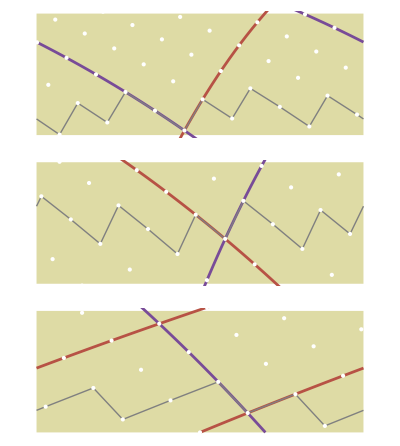

```mathematica
Ch5Transition
```

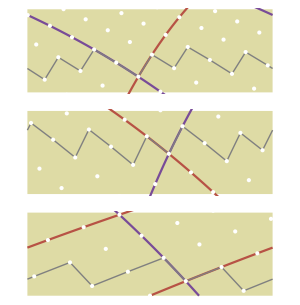
```mathematica
(*shExport[Ch5Transition]
-Graphics-*)
```

## Ch5Transforms Disk Transforms

```mathematica
quadraticScaling[scale_] :=  Function[{z}, Ramp@Re@Sqrt[1- scale * z ]];
exponentialScaling :=  Function[{z}, Exp[- 2π z ]];
interScaling[scale_] := Function[{z},
quadraticScaling[scale][z]*exponentialScaling[z]]

quadraticDiskLattice[lattice_] := Module[{diskscaling,res ,scale},
scale =  10;
diskscaling = Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = quadraticScaling[scale][z];
r * { Cos[2 π x], Sin[2π x]} 
]];

res =  latticeSetCylinderLU[lattice,{0, 1/scale}];
res =  latticeSetScaling[res,"Disk"->diskscaling];

res
];
logarithmicDiskLattice[lattice_] := Module[{zMin,zMax,res },

{zMin,zMax}  = latticeGetCylinderLU[lattice];
res =  latticeSetCylinderLU[lattice,{0,zMax}];

res =  latticeSetScaling[res,"Disk"->Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = exponentialScaling[z];
r * { Cos[2 π x], Sin[2π x]} 
]]];
res
];
intermediateDiskLattice[lattice_] := Module[{diskscaling,escaling,res ,scale},
scale =  10;
diskscaling = Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = interScaling[scale][z];
r * { Cos[2 π x], Sin[2π x]} 
]];

res =  latticeSetCylinderLU[lattice,{0, 1/scale}];
res =  latticeSetScaling[res,"Disk"->diskscaling];

res

];
```

```mathematica
diskParastichyPlot[lattice_,m_,k_,style_] := Module[{func},
(*func =latticeDiskParastichyFunction[lattice,m,k];
*)
func =  First@latticeParastichyFunctions[lattice,m,k,"Disk"];
ParametricPlot[func[t],{t,0,1},PlotStyle->style]
];

diskParastichyLine[lattice_,central_] := Module[{g,disk},
disk = latticeGraphicRegion[lattice,"Disk"];
g = Show[
Graphics[
{
{figureStyle["CylinderColour"],disk
}
}
,PlotRange->RegionBounds[disk] * central
]
,MapIndexed[diskParastichyPlot[lattice,#1,0,Directive[Thick,diskParastichyColours@First[#2]]]&,Take[diskParastichyMN,2]]
,Graphics[
{
{White,Point[latticePoints[lattice,"Disk"]]}
}
]
];
g
];

diskSeeds[lattice_,voronoi_,central_] := Module[{g,mnList,disk,diskPoints,inner,outer,v},
disk = latticeGraphicRegion[lattice,"Disk"];
diskPoints = latticePoints[lattice,"Disk"];


g = Show[
Graphics[
{
{figureStyle["CylinderColour"],disk}}
,PlotRange->RegionBounds[disk] * central
]
,MapIndexed[diskParastichyPlot[lattice,#1,0,Directive[Thick,diskParastichyColours@First[#2]]]&,diskParastichyMN]

,Graphics[
{
{FaceForm[None],EdgeForm[Gray],voronoi}
}
]
];
g
];
```

```mathematica
makeVoronoi[lattice_] := Module[{disk,diskPoints,inner,outer,v},
disk = latticeGraphicRegion[lattice,"Disk"];
{inner,outer} = If[Head[disk]===Disk,
(* disk *) {Missing[],disk⟦2⟧},
(* annulus *)  disk⟦2⟧];
diskPoints = latticePoints[lattice,"Disk"];
vClipList = MeshPrimitives[VoronoiMesh[latticePoints[lattice,"Disk"]],2];
outerDisk = DiscretizeRegion[Disk[{0,0},outer*0.99]];
vClipList = Map[RegionIntersection[outerDisk,#]&,vClipList];
If[!MissingQ[inner],
innerDisk = DiscretizeRegion[Disk[{0,0},inner]];
vClipList = Map[RegionDifference[#,innerDisk]&,vClipList];
];
vClipList
];
makeVoronoiDiskLines[lattice_] := Module[{disk,diskPoints,inner,outer,v},
disk = latticeGraphicRegion[lattice,"Disk"];
{inner,outer} = If[Head[disk]===Disk,
(* disk *) {Missing[],disk⟦2⟧},
(* annulus *)  disk⟦2⟧];
diskPoints = latticePoints[lattice,"Disk"];
vClipList = Line[MeshPrimitives[VoronoiMesh[latticePoints[lattice,"Disk"]],1] /. Line[x_]->x];
outerDisk = DiscretizeRegion[Disk[{0,0},outer*0.99]];
vClipList =RegionIntersection[outerDisk,vClipList];
If[!MissingQ[inner],
innerDisk = DiscretizeRegion[Disk[{0,0},inner]];
vClipList = RegionDifference[vClipList,innerDisk];
];
MeshPrimitives[vClipList,1]
];


makedisks := If[rebuildingData, Module[{nPoints,rise},
nPoints = 1500;
rise = 0.0001;
goldenLattice200 = latticeCreateDH[{GoldenAngle/(2π),rise},{0,rise*nPoints}];

latticeLN =logarithmicDiskLattice[goldenLattice200];
latticeEA =quadraticDiskLattice[goldenLattice200];
latticeIM=intermediateDiskLattice[goldenLattice200];
voronoiLN = makeVoronoiDiskLines[latticeLN];
voronoiEA = makeVoronoiDiskLines[latticeEA];
voronoiIM = makeVoronoiDiskLines[latticeIM];
store= getTextbookData["Ch5DiskVoronoi"];
If[MissingQ[store],store=<||>];
store = Append[store,"LN"-> <|"Lattice"-> latticeLN,"Voronoi"->voronoiLN|>];
store = Append[store,"EA"-> <|"Lattice"-> latticeEA,"Voronoi"->voronoiEA|>];
store = Append[store,"IM"-> <|"Lattice"-> latticeIM,"Voronoi"->voronoiIM|>];
setTextbookData["Ch5DiskVoronoi",store];

],
Module[{store},
store= getTextbookData["Ch5DiskVoronoi"];
latticeLN= store["LN"]["Lattice"];
voronoiLN = store["LN"]["Voronoi"];
latticeEA = store["EA"]["Lattice"];
voronioEA=store["EA"]["Voronoi"];
]
]

Module[{store},If[rebuildingData,
store= getTextbookData["Ch5DiskVoronoi"];
If[MissingQ[store],store=<||>];
makedisks[];
store = Append[store,"LN"-> <|"Lattice"-> latticeLN,"Voronoi"->voronoiLN|>];
store = Append[store,"EA"-> <|"Lattice"-> latticeEA,"Voronoi"->voronoiEA|>];
setTextbookData["Ch5DiskVoronoi",store];
]];

diskParastichyMN =  Reverse@{21,34,55,89};
diskParastichyColours  =   <|1->jParastichyColour[1],2->jParastichyColour[2],3->jParastichyColour[3],4->Black|>;
```

```mathematica
makeCh5Transforms := Module[{central},
makedisks;
central = 1.01;
GraphicsColumn[{
GraphicsRow[{
diskParastichyLine[latticeLN,central],diskParastichyLine[latticeEA,central]
}
],
GraphicsRow[
{diskSeeds[latticeLN,voronoiLN,central],diskSeeds[latticeEA,voronioEA,central]}]
}]
];
```

```mathematica
setGill = Directive[FontFamily->jStyle["FontFamily"],FontSize->14];
setBaseGill = BaseStyle->setGill;

legendText = Map[Style[#,setGill]&,ToString/@Reverse@diskParastichyMN];
gLabel = Graphics[
{Text["Logarithmic spiral",Scaled[{0.275,1}],{0,1}],
,Text["Equal area",Scaled[{0.725,1}],{0,1}]
}
];
```

```mathematica
Ch5Transforms := 
Show[Legended[
Show[{makeCh5Transforms, gLabel}]
,Placed[LineLegend[Reverse@Values[diskParastichyColours],legendText],{{1/2,1/2},{1/2,1/2}}]
]
,BaseStyle->setGill
];
```

```mathematica
Ch5Transforms
```

-Graphics-

```mathematica
jExport@Ch5Transforms
```

-Graphics-

```mathematica
diskParastichyColours
```

<|1→RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],2→RGBColor[0.4687348547943994, 0.29473626986998797, 0.5955133155492501],3→RGBColor[0.4518714536621338, 0.549629484806721, 0.24743503166788056],4→GrayLevel[0]|>

```mathematica
(*Show[Ch5Transforms]*)
```

```mathematica
Map[sunParaColours[[#StyleIndex]]&,paraData]
```

{RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0., 0., 0.],RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],RGBColor[0.4687348547943994, 0.29473626986998797, 0.5955133155492501],RGBColor[0.4518714536621338, 0.549629484806721, 0.24743503166788056],GrayLevel[0]}

```mathematica
Ch5Sunflower := Legended[sunflowerSeeds[latticeIM,voronoiIM,central],
Placed[
LineLegend[
Map[sunParaColours[[#StyleIndex]]&,paraData]
,Map[#Parastichy&,paraData]
,LabelStyle->jFont[12]
],{{1,1},{1,1}}]]
```

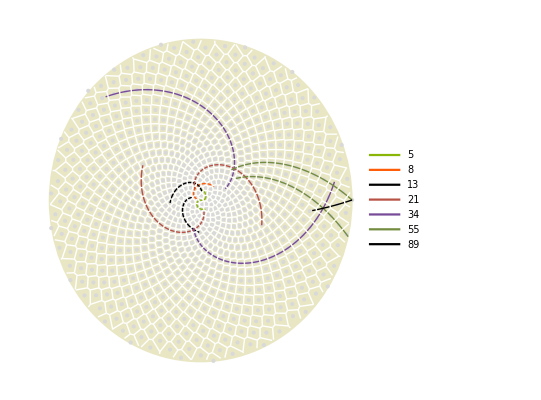

```mathematica
jExport[Ch5Sunflower]
```

```mathematica
sunParaColours = Join[Values@diskParastichyColours,Part[ColorData[3,"ColorList"],{1,2,4}]];
sunflowerParastichyPlot[lattice_,m_,kRange_,styleIndex_,tRange_] := Module[{func,plot},
func[k_]:=  First@latticeParastichyFunctions[lattice,m,k,"Disk"];
plot[k_]:= ParametricPlot[func[k][t],{t,tRange[[1]],tRange[[2]]}
,PlotStyle->Directive[Thick,sunParaColours[[styleIndex]]]
];
Map[plot,kRange]
];

paraData = {
<|"Parastichy"->5,"k"->{70,68},"StyleIndex"->7,"tRange"->{0.985,1}|>
,<|"Parastichy"->8,"k"->{68},"StyleIndex"->6,"tRange"->{0.95,0.999}|>
,<|"Parastichy"->13,"k"->{50,40},"StyleIndex"->5,"tRange"->{0.88,0.99}|>
,<|"Parastichy"->21,"k"->{70,38},"StyleIndex"->1,"tRange"->{0.6,.98}|>
,<|"Parastichy"->34,"k"->{70,48},"StyleIndex"->2,"tRange"->{0.1,0.9}|>
,<|"Parastichy"->55,"k"->{0,53},"StyleIndex"->3,"tRange"->{0,.8}|>
,<|"Parastichy"->89,"k"->{0},"StyleIndex"->4,"tRange"->{0,0.25}|>
};


sunflowerSeeds[lattice_,voronoi_,central_] := Module[{g,mnList,disk,diskPoints,inner,outer,v},
disk = latticeGraphicRegion[lattice,"Disk"];
diskPoints = latticePoints[lattice,"Disk"];

g = Show[
Graphics[
{
{Lighter@figureStyle["CylinderColour"],disk}}
,PlotRange->RegionBounds[disk] * central
]
,Graphics[
{
{LightGray,Point[diskPoints]}
}
]
,Map[sunflowerParastichyPlot[lattice,#Parastichy,#k,#StyleIndex,#tRange]&,paraData]

,Graphics[
{
{White,voronoi}
}
]
];
g
];
```

## Stem bulge

```mathematica
smoothRadiusFunctionV[radiusF_,nPoints_:20] := Module[{stemPoints,radiusFunction},
(* helper smooth function for v in [0,1] *)stemPoints = Table[radiusF[v/nPoints],{v,0,nPoints}];radiusFunction=BSplineFunction[stemPoints];
radiusFunction
];
bulgeFromPoints [pts_] :=  smoothRadiusFunctionV@Function[h,Interpolation[ Reverse /@pts,InterpolationOrder->1][h]];

Module[{rmin,rmax},
rmin = 1/20;
rmax = 6;
smoothBulgyV = bulgeFromPoints[ {{1,0},{1,0.4},{1,0.7},{rmax,0.8},{rmin,1}}];
widenV = bulgeFromPoints[ {{1,0},{1,1/20},{rmax,3/20},{rmax,1}}];

];
```

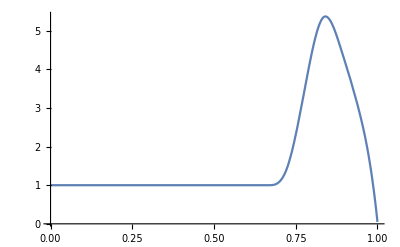

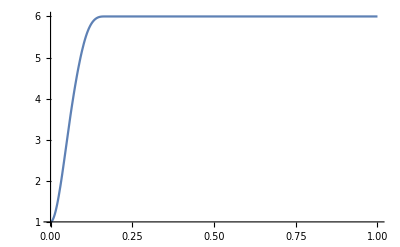

```mathematica
Plot[smoothBulgyV[v],{v,0,1},PlotRange->All]
Plot[widenV[v],{v,0,1},PlotRange->All]
```

```mathematica
scaleZ01ToCylinder[cylinderLU_,bulgeFunction_] := Module[{zScale},
zScale[cylinderZ_] :=   (cylinderZ-cylinderLU[[1]])/(cylinderLU[[2]]-cylinderLU[[1]]);
Composition[bulgeFunction,zScale]
];
```

```mathematica
makeBulgeLattice[lattice_,bulgeFunction_,bulgeMax_] := Module[{bulgedXZ,bulgeLattice,cylinder},
bulgeLattice =lattice;
bulgedXZ [{x_,z_}] := { x * scaleZ01ToCylinder[latticeGetCylinderLU[bulgeLattice],bulgeFunction][z],z};
bulgeLattice = latticeSetScaling[bulgeLattice,"StemBulge"->bulgedXZ];
bulgeLattice = latticeSetScaling[bulgeLattice,"StemBulgeZ01"->bulgeFunction];
cylinder= latticeGetCylinder[bulgeLattice];
cylinder[[1]] = bulgeMax*cylinder[[1]] ;
bulgeLattice= latticeSetDisplayCylinder[bulgeLattice,cylinder];
bulgeLattice
];
```

```mathematica
extendLatticePoints[lattice_] := Module[{bulgeXZ,lPoints,rises,widthAtRises},
bulgeXZ = latticeScaling[lattice,"StemBulge"];
lPoints = latticePoints[lattice,"StemBulge"];
rises  = Last /@lPoints;
widthAtRises= Map[{2 * First@ bulgeXZ[{1/2,#}],0}&,rises];
Flatten[{lPoints-widthAtRises,lPoints,lPoints+widthAtRises},1]
];

voronoiLines[points_,region_] := Module[{vClipList},
vClipList = Line[MeshPrimitives[VoronoiMesh[points],1] /. Line[x_]->x];
RegionIntersection[region,vClipList]
];

bulgeVoronoiLines[lattice_] := Module[{eLPoints},
eLPoints = extendLatticePoints[lattice];
 voronoiLines[eLPoints,latticeGraphicRegion[lattice,"StemBulge"]]
];
```

## Pineapple

```mathematica
pmax=5;
pineappleV = bulgeFromPoints[ 
{{1,0},{1,0.3},{pmax,0.35},{pmax,0.8},{1,0.9},{1,1}}];
```

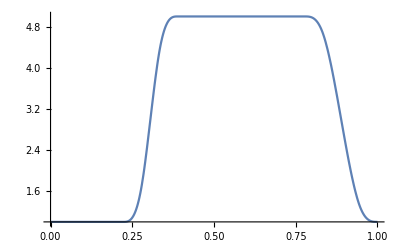

```mathematica
Plot[pineappleV[v],{v,0,1}]
```

```mathematica
makePineapple[rise_] := Module[{nPoints},
nPoints = 250;
pineappleLattice = makeBulgeLattice[latticeCreateDH[{N@GoldenAngle/(2 π),rise},{0,rise*nPoints}],pineappleV,6];
pineappleLattice
];
pineappleLattice = makePineapple[0.030];

parametricPineappleV[s_] := Module[{scaleV},
scaleV:= Function[{v},(1-s)  + s  pineappleV[v]];
scaleV
];
rise =0.03 ;
nPoints = 250;

parametricPineapple[s_] := makeBulgeLattice[
latticeCreateDH[{N@GoldenAngle/(2 π),rise},{0,rise*nPoints}],parametricPineappleV[s]
,6
];
```

```mathematica
Ch5PineappleVoronoi := Show[makePineappleVoronoi[pineappleLattice,{5,8}]]
```

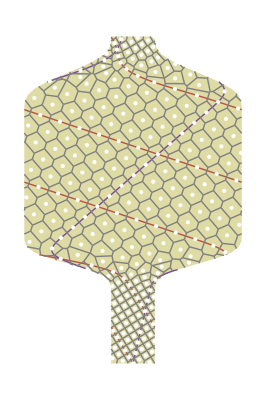

```mathematica
Ch5PineappleVoronoi
```

```mathematica
makePineappleVoronoi[lattice_,mList_] := Module[{voronoiBulge,g},
voronoiBulge = bulgeVoronoiLines[lattice];

g=Show[
Graphics[{
{figureStyle["CylinderColour"],latticeGraphicRegion[lattice,"StemBulge"]}}
],
MapIndexed[bulgeParastichyPlot[lattice,#1,0,Directive[Thick,diskParastichyColours@First[#2]]]&,mList]
,
Graphics[{
{White,Point[latticePoints[lattice,"StemBulge"]]}
,{Gray,voronoiBulge}
}],
Axes->False
];
g
];
bulgeParastichyPlot[lattice_,m_,k_,style_] := Map[ParametricPlot[#[s],{s,0,1},PlotStyle->style]&,latticeParastichyFunctions[lattice,m,k,"StemBulge"]]

makeGraphicPineapple[lattice_,mList_] := Module[{voronoiBulge,g},

g={
Graphics[{
{figureStyle["CylinderColour"],latticeGraphicRegion[lattice,"StemBulge"]}}
],
MapIndexed[bulgeParastichyPlot[lattice,#1,0,Directive[Thick,diskParastichyColours@First[#2]]]&,mList]
,
Graphics[{
{White,Point[latticePoints[lattice,"StemBulge"]]}
}]
};
g
];
```

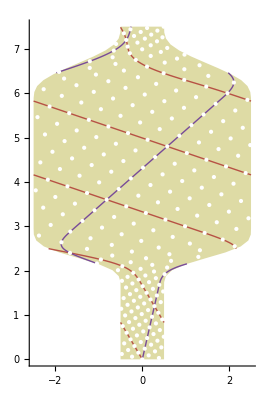

```mathematica
Show[makeGraphicPineapple[parametricPineapple[1],{5,8}],Axes->True]
```

```mathematica
pineFrame[s_] := Show[makeGraphicPineapple[parametricPineapple[s],{5,8}],
PlotRange->{ {-2.6,2.6},{0,7.5}},Axes->False];
pineFrameV[s_] := Show[makePineappleVoronoi[parametricPineapple[s],{5,8}],
PlotRange->{ {-2.6,2.6},{0,7.5}},Axes->False]

pineFrameSet = {pineFrame[0],pineFrame[.2],pineFrame[1]};
```

```mathematica
If[rebuildingData,
pineFrameVSet = {pineFrameV[0],pineFrameV[.2],pineFrameV[1]};
setTextbookData["Ch5PineFrameVSet",pineFrameVSet];
];
```

```mathematica
pineFrameVSet = getTextbookData["Ch5PineFrameVSet"];
showPineSet  :=Legended[GraphicsRow[pineFrameVSet,Frame->All,FrameStyle->LightGray],
Placed[
Framed[
LineLegend[ {jParastichyColour[1],jParastichyColour[2]},{5,8},LabelStyle->setGill]
,Background->White
]
,{{1/3,.9},{1/2,1}}]
];

Ch5PineSet  := showPineSet
```

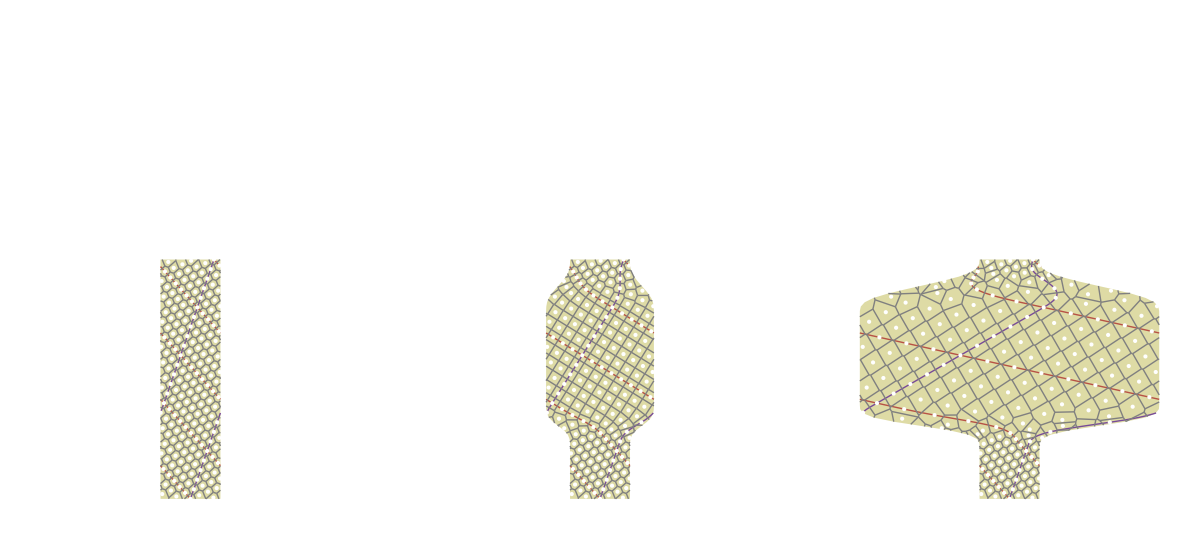

```mathematica
Ch5PineSet
```

```mathematica
graphics2DTo3D[g_] := Module[{xy23,g23,res},
xy23[{x_,y_}] := {x,0,y};
g23[Polygon[x___]] := Polygon[Map[xy23,x]];
g23[line_Line] :=  Map[ xy23,line,{2}] /; VectorQ[line[[1,1]]];
g23[line_Line] :=  Map[ xy23,line,{3}];  
g23[Point[x___]] := Point[Map[xy23,x]]; 
g23[x_] := x;
res = Map[g23,List@@g,Infinity];
(*res = res /. jStyle["CylinderColour"]-> jStyle["CylinderColour3D"]
*)
res];
```

```mathematica
pv = Last[pineFrameVSet];
pineappleV3 = graphics2DTo3D[pv];
Graphics3D[pineappleV3]
```

-Graphics3D-

## Make pineapple 3 d

```mathematica
pineappleStem = stemAddShape[pineappleLattice,pineappleV,0.5];
stem=pineappleStem;
```

```mathematica
Show[showPineapple3D[pineappleStem,{2}],"Lighting"->"Neutral"]
```

-Graphics3D-

```mathematica
surfacePlot[stem_,vclip_] := Module[{shapeFunctionUV=stemShapeFunctionUV[stem]},ParametricPlot3D[ shapeFunctionUV[u,v],{u,0,1},{v,0,vclip}
,PlotStyle-> Directive[figureStyle["CylinderColour"],Opacity[1]]
,Mesh->None,Axes->None]
];
showStemBase[stem_] := Module[{cylinderL,cylinderU,baseHeight,base},
{cylinderL,cylinderU} = latticeGetCylinderLU[stem];
baseHeight = 0.05 * (cylinderU-cylinderL);
base = {Opacity[0.5],FaceForm[Brown],Cylinder[{{0,0,cylinderL-baseHeight},{0,0,cylinderL}},stemRadiusFunctionV[stem][0]]};
base
];

showStemParastichy[stem_,mList_] := Module[{},
MapIndexed[
(ParametricPlot3D[stemParastichyOfV[stem,#1,1][v],{v,0,1}
,PlotStyle->figureStyle["ParastichyColour"][First[#2]]
])&,mList]
];

showStemPoints[stem_] := Module[{},
Point[Values@stemPoints[stem]]
];

showStemPointNames[stem_] := Module[{},
KeyValueMap[Text[#1,#2]&,stemPoints[stem]]
];


showPineapple3D[stem_,mList_] := Module[{g,surface,base,displayCylinder,radius,rmax},
displayCylinder = latticeGetCylinder[stem];

base = showStemBase[stem] ;
surface = surfacePlot[stem,1];
g=Show[
Graphics3D[base,
PlotRange-> {displayCylinder⟦1⟧,displayCylinder⟦1⟧,displayCylinder⟦2⟧}]
,surface
,Graphics3D[{White,PointSize[Large],showStemPoints[stem]}]
, showStemParastichy[stem,mList]
,Axes->True
];
g
];
```

## Two way stretch

```mathematica
(*nPoints = 200;
rise = 0.02;
goldenLattice200 = latticeCreateDH[{GoldenAngle/(2π),rise},{0,rise*nPoints}];
riseScaling[z_] := quadraticRiseFallZLattice[goldenLattice200,z]
risingPhyllotaxisLatticeQuadratic = makeStretchedLattice[goldenLattice200,riseScaling];
*)
```